```mathematica
basedir="d:\\data\\cycle 193\\TEST-3285\\rawdata\\sc\\"
Get[basedir<>"..\\camera_ifg.m"]
minIntens=2000;  (* Schwellenwert zur Unterdrückung schwach beleuchtetet Randbereiche der Kamera *)
(*
loadimage[basedir<>filename]    liefert Array mit den einzelnen Bildern aus der Tiff-Datei.;
fittile[images_,tileDX_,tileDY_,nx_,ny_,minIntensity_,period_]

*)
```

d:\data\cycle 193\TEST-3285\rawdata\sc\

```mathematica
StringLength[""]
```

0

```mathematica
LoadDatFile[filename_]:=  ToExpression[Transpose[StringSplit[#,"\t"] & /@ Pick[#,StringMatchQ[#,{"\\**","[*"," *","\t*",""}],False]&@Import[basedir<>filename,"lines"]]]
```

```mathematica
reduceSlotsBy[img_,its_,slotmax_]:=Module[{maxph,maxtim},
maxtim=slotmax/its;
maxph=Length[img]/(slotmax+2);
Flatten[Table[    Join[{img[[1+(ph-1)*(slotmax+2)]]},Table[Total[img[[(ph-1)*(slotmax+2)+1+(tim-1)*its;;(ph-1)*(slotmax+2)+tim*its]],1],{tim,1,maxtim}],{img[[ph*(slotmax+2)]]}]     ,{ph,1,maxph}],1]
]
```

```mathematica
(* alle Bilder eines Multi-Page-Images aufsummieren und auf die Anzahl der nicht leeren Pixel normieren *)
integrateImg[img_]:=(Total[#,2]&/@img)   / Count[Flatten[Total[img]],x_/;x>10]
```

# 2-lamella crystal, polished side

```mathematica
filename = "rocking_cam_24May1106.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; Dimensions[img]
```

{41,64,50}

```mathematica
ArrayPlot[img[[20]],ColorFunction->GrayLevel]  (* upside down! *)
```

-Graphics-

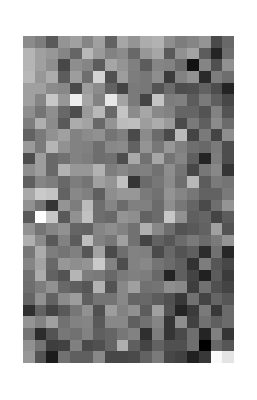
-Graphics--Graphics--Graphics-

```mathematica
imgbaseback=img[[1;;Length[img],36;;62,5;;16]];
imgbaseside=img[[1;;Length[img],36;;63,20;;37]];
imglamella=img[[1;;Length[img],2;;32,9;;20]];
Row[{ArrayPlot[imgbaseback[[20]],ColorFunction->GrayLevel],ArrayPlot[imgbaseside[[20]],ColorFunction->GrayLevel],ArrayPlot[imglamella[[20]],ColorFunction->GrayLevel]}]
```

```mathematica
baseback=integrateImg[imgbaseback];
baseside=integrateImg[imgbaseside];
lamella=integrateImg[imglamella];
theta=LoadDatFile[StringTake[filename,StringLength[filename]-3]<>"dat"] [[2]];
```

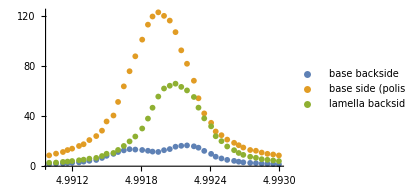

```mathematica
ListPlot[{Transpose[{theta,baseback}],Transpose[{theta,baseside}],Transpose[{theta,lamella}]},ImageSize->300, PlotLegends->{"base backside","base side (polished)","lamella backside"}]
```

```mathematica
(* fitGauss[fitdata_]:=NonlinearModelFit[Transpose[{theta,fitdata}], a + b*(Exp[-(x-c)^2/(2 d^2)]),{{a,0},{b,100},{c,theta[[Floor[Length[theta]/2]]]},{d,(theta[[Length[theta]]]-theta[[1]])/4}},x] *)
```

```mathematica
fitbase=fitGauss[Transpose[{theta,baseside}],0.25]
fitbase["ParameterTable"]
fwhmbase=fitbase["ParameterTableEntries"][[3,1]] * 2 * √Log[2]
posbase=fitbase["ParameterTableEntries"][[2,1]]
```

FittedModel[121.09 ⅇ^(-6.62121×10^6 (-4.99196+«26»)^2)]

| Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 121.09 | 0.984859 | 122.951 | 3.06796×10^-25
CameraIfgPackage`Private`c | 4.99196 | 2.64817×10^-6 | 1.88506×10^6 | 3.31776×10^-92
CameraIfgPackage`Private`d | 0.0002748 | 3.0884×10^-6 | 88.9779 | 5.38166×10^-23

0.000457571

4.99196

```mathematica
fitlamella=fitGauss[Transpose[{theta,lamella}],0.25]
fitlamella["ParameterTable"]
fwhmlamella=fitlamella["ParameterTableEntries"][[3,1]] * 2 * √Log[2]
poslamella=fitlamella["ParameterTableEntries"][[2,1]]
```

FittedModel[65.8216 ⅇ^(-8.17658×10^6 (-4.9921+«26»)^2)]

| Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 65.8216 | 0.712001 | 92.4459 | 6.56042×10^-21
CameraIfgPackage`Private`c | 4.9921 | 3.1038×10^-6 | 1.60838×10^6 | 2.84816×10^-80
CameraIfgPackage`Private`d | 0.000247286 | 3.70477×10^-6 | 66.7479 | 6.20804×10^-19

0.000411758

4.9921

```mathematica
(* Theorie: y=0 für Si220 bei 30° ergibt ein dtheta von 0.000161°  *)
(poslamella-posbase)
(poslamella-posbase) /  ((fwhmlamella+fwhmbase)/2)
```

0.000143284

0.329644

# 2-lamella crystal, polished side, run 2

```mathematica
filename = "rocking_cam_24May1152.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; Dimensions[img]
```

{41,64,50}

```mathematica
ArrayPlot[img[[20]],ColorFunction->GrayLevel]  (* upside down! *)
```

-Graphics-

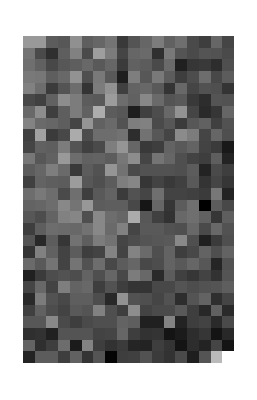
-Graphics--Graphics--Graphics-

```mathematica
imgbaseback=img[[1;;Length[img],36;;62,5;;16]];
imgbaseside=img[[1;;Length[img],36;;63,20;;37]];
imglamella=img[[1;;Length[img],2;;32,9;;20]];
Row[{ArrayPlot[imgbaseback[[20]],ColorFunction->GrayLevel],ArrayPlot[imgbaseside[[20]],ColorFunction->GrayLevel],ArrayPlot[imglamella[[20]],ColorFunction->GrayLevel]}]
```

```mathematica
baseback=integrateImg[imgbaseback];
baseside=integrateImg[imgbaseside];
lamella=integrateImg[imglamella];
theta=LoadDatFile[StringTake[filename,StringLength[filename]-3]<>"dat"] [[2]];
```

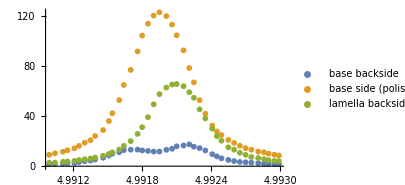

```mathematica
ListPlot[{Transpose[{theta,baseback}],Transpose[{theta,baseside}],Transpose[{theta,lamella}]},ImageSize->300, PlotLegends->{"base backside","base side (polished)","lamella backside"}]
```

```mathematica
fitbase=fitGauss[Transpose[{theta,baseside}],0.25]
fitbase["ParameterTable"]
fwhmbase=fitbase["ParameterTableEntries"][[3,1]] * 2 * √Log[2]
posbase=fitbase["ParameterTableEntries"][[2,1]]
```

FittedModel[121.396 ⅇ^(-6.59545×10^6 (-«18»+«26»)^2)]

| Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 121.396 | 0.747902 | 162.316 | 3.61661×10^-27
CameraIfgPackage`Private`c | 4.99195 | 1.96265×10^-6 | 2.54348×10^6 | 2.74922×10^-94
CameraIfgPackage`Private`d | 0.000275336 | 2.31656×10^-6 | 118.855 | 5.27293×10^-25

0.000458464

4.99195

```mathematica
fitlamella=fitGauss[Transpose[{theta,lamella}],0.25]
fitlamella["ParameterTable"]
fwhmlamella=fitlamella["ParameterTableEntries"][[3,1]] * 2 * √Log[2]
poslamella=fitlamella["ParameterTableEntries"][[2,1]]
```

FittedModel[65.9408 ⅇ^(-8.09851×10^6 (-«18»+«26»)^2)]

| Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 65.9408 | 0.491502 | 134.162 | 3.5892×10^-23
CameraIfgPackage`Private`c | 4.99209 | 2.15516×10^-6 | 2.31635×10^6 | 1.72491×10^-82
CameraIfgPackage`Private`d | 0.000248475 | 2.56409×10^-6 | 96.9055 | 3.39547×10^-21

0.000413738

4.99209

```mathematica
(* Theorie: y=0 für Si220 bei 30° ergibt ein dtheta von 0.000161°  *)
(poslamella-posbase)
(poslamella-posbase) /  ((fwhmlamella+fwhmbase)/2)
```

0.00014156

0.345486

# 2-lamella crystal, etched side

```mathematica
filename = "rocking_cam_24May1629.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; Dimensions[img]
```

{41,64,50}

```mathematica
ArrayPlot[img[[20]],ColorFunction->GrayLevel]  (* upside down! *)
```

-Graphics-

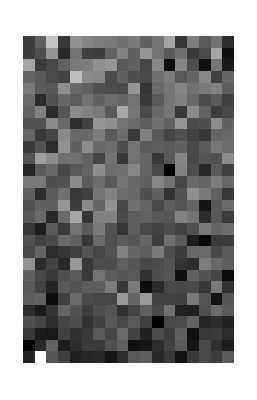
-Graphics--Graphics--Graphics-

```mathematica
imgbaseback=img[[1;;Length[img],36;;62,4;;15]];
imgbaseside=img[[1;;Length[img],36;;63,18;;35]];
imglamella=img[[1;;Length[img],2;;32,4;;16]];
Row[{ArrayPlot[imgbaseback[[20]],ColorFunction->GrayLevel],ArrayPlot[imgbaseside[[20]],ColorFunction->GrayLevel],ArrayPlot[imglamella[[20]],ColorFunction->GrayLevel]}]
```

```mathematica
baseback=integrateImg[imgbaseback];
baseside=integrateImg[imgbaseside];
lamella=integrateImg[imglamella];
theta=LoadDatFile[StringTake[filename,StringLength[filename]-3]<>"dat"] [[2]];
```

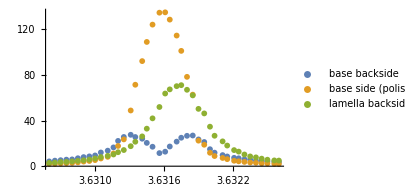

```mathematica
ListPlot[{Transpose[{theta,baseback}],Transpose[{theta,baseside}],Transpose[{theta,lamella}]},ImageSize->300, PlotLegends->{"base backside","base side (polished)","lamella backside"}]
```

```mathematica
fitbase=fitGauss[Transpose[{theta,baseside}],0.25]
fitbase["ParameterTable"]
fwhmbase=fitbase["ParameterTableEntries"][[3,1]] * 2 * √Log[2]
posbase=fitbase["ParameterTableEntries"][[2,1]]
```

FittedModel[136.067 ⅇ^(-1.19462×10^7 (-«19»+«26»)^2)]

| Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 136.067 | 1.10421 | 123.226 | 7.75372×10^-16
CameraIfgPackage`Private`c | 3.63159 | 1.98625×10^-6 | 1.82837×10^6 | 2.22999×10^-53
CameraIfgPackage`Private`d | 0.000204583 | 2.69836×10^-6 | 75.8177 | 6.11161×10^-14

0.000340653

3.63159

```mathematica
fitlamella=fitGauss[Transpose[{theta,lamella}],0.25]
fitlamella["ParameterTable"]
fwhmlamella=fitlamella["ParameterTableEntries"][[3,1]] * 2 * √Log[2]
poslamella=fitlamella["ParameterTableEntries"][[2,1]]
```

FittedModel[70.1446 ⅇ^(-9.10388×10^6 (-«18»+«26»)^2)]

| Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 70.1446 | 0.997634 | 70.311 | 3.0036×10^-19
CameraIfgPackage`Private`c | 3.63173 | 3.9425×10^-6 | 921173. | 6.97018×10^-77
CameraIfgPackage`Private`d | 0.000234354 | 4.50407×10^-6 | 52.0315 | 2.00257×10^-17

0.000390225

3.63173

```mathematica
(* Theorie: y=0 für Si220 bei 30° ergibt ein dtheta von 0.000161°  *)
(poslamella-posbase)
(poslamella-posbase) /  ((fwhmlamella+fwhmbase)/2)
```

0.000142882

0.419183

```mathematica
ListPlot[{Transpose[{theta,baseback}],Transpose[{theta,baseside}],Transpose[{theta,lamella}]},ImageSize->300, PlotLegends->{"base backside","base side (polished), FWHM="<>ToString[fwhmbase],"lamella backside,      FWHM="<>ToString[fwhmlamella]}]
```

-Graphics-

# 1-lamella crystal, etched side

```mathematica
filename = "rocking_25May0051.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; Dimensions[img]
theta=LoadDatFile[StringTake[filename,StringLength[filename]-3]<>"dat"] [[2]];
```

{51,64,64}

```mathematica
ArrayPlot[img[[20]],ColorFunction->GrayLevel]  (* upside down! *)
```

-Graphics-

```mathematica
imglamella=img[[1;;Length[img],18;;50,7;;58]]; Dimensions[imglamella]
Row[{ArrayPlot[imglamella[[20]],ColorFunction->GrayLevel]}]
```

{51,33,52}

-Graphics-

```mathematica
res=fitgridGauss[imglamella,theta,4,4,0,0.25]; Dimensions[res]
```

{8,13,6}

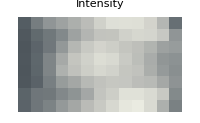
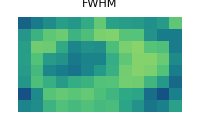
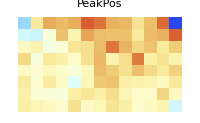

```mathematica
plotresGauss[res,200,0.0001,0.00002]
```

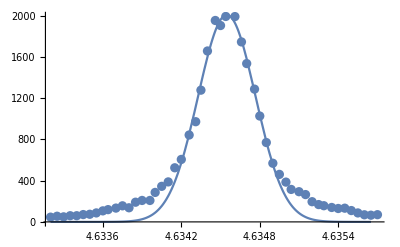

```mathematica
tilex=8; tiley=5;
Show[{ListPlot[res[[tiley,tilex,1]]],Plot[res[[tiley,tilex,2]][x],{x,theta[[1]],theta[[Length[theta]-1]]}]}]
```

```mathematica
filename = "rocking_25May0224.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; Dimensions[img]
theta=LoadDatFile[StringTake[filename,StringLength[filename]-3]<>"dat"] [[2]];
```

{51,64,64}

```mathematica
ArrayPlot[img[[20]],ColorFunction->GrayLevel]  (* upside down! *)
```

-Graphics-

```mathematica
imglamella=img[[1;;Length[img],18;;50,7;;58]]; Dimensions[imglamella]
Row[{ArrayPlot[imglamella[[20]],ColorFunction->GrayLevel]}]
```

{51,33,52}

-Graphics-

```mathematica
res2=fitgridGauss[imglamella,theta,4,4,0,0.25]; Dimensions[res]
```

{8,13,6}

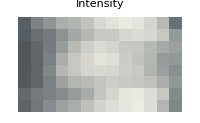
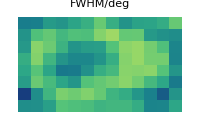
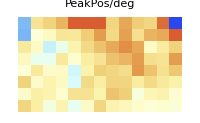

```mathematica
plotresGauss[res2,200,0.0001,0.00002]
```

```mathematica
filename = "rocking_25May0357.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; Dimensions[img]
theta=LoadDatFile[StringTake[filename,StringLength[filename]-3]<>"dat"] [[2]];
```

{51,64,64}

```mathematica
ArrayPlot[img[[20]],ColorFunction->GrayLevel]  (* upside down! *)
```

-Graphics-

{51,33,52}

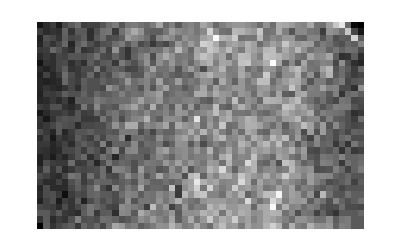

```mathematica
imglamella=img[[1;;Length[img],18;;50,7;;58]]; Dimensions[imglamella]
Row[{ArrayPlot[imglamella[[20]],ColorFunction->GrayLevel]}]
```

```mathematica
res3=fitgridGauss[imglamella,theta,4,4,0,0.25]; Dimensions[res]
```

{8,13,6}

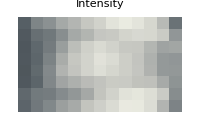
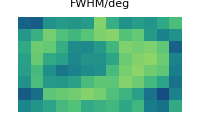
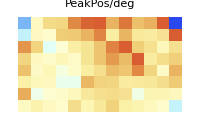

```mathematica
plotresGauss[res3,200,0.0001,0.00002]
```

```mathematica
filename = "rocking_25May0529.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; Dimensions[img]
theta=LoadDatFile[StringTake[filename,StringLength[filename]-3]<>"dat"] [[2]];
```

{51,64,64}

```mathematica
ArrayPlot[img[[20]],ColorFunction->GrayLevel]  (* upside down! *)
```

-Graphics-

```mathematica
res4=fitgridGauss[imglamella,theta,4,4,0,0.25]; Dimensions[res]
```

{8,13,6}

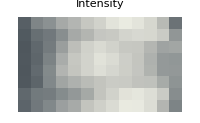
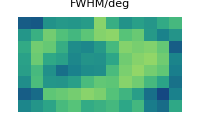
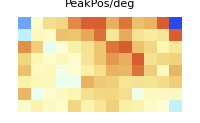

```mathematica
plotresGauss[res4,200,0.0001,0.00002]
```

```mathematica
filename = "rocking_25May0702.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; Dimensions[img]
theta=LoadDatFile[StringTake[filename,StringLength[filename]-3]<>"dat"] [[2]];
```

{51,64,64}

```mathematica
ArrayPlot[img[[20]],ColorFunction->GrayLevel]  (* upside down! *)
```

-Graphics-

```mathematica
imglamella=img[[1;;Length[img],18;;50,7;;58]]; Dimensions[imglamella]
Row[{ArrayPlot[imglamella[[20]],ColorFunction->GrayLevel]}]
```

{51,33,52}

-Graphics-

```mathematica
res5=fitgridGauss[imglamella,theta,4,4,0,0.25]; Dimensions[res5]
```

{8,13,6}

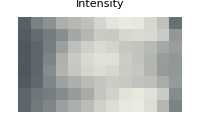
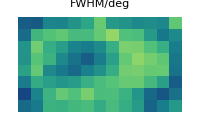
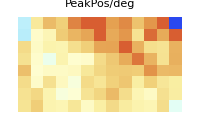

```mathematica
plotresGauss[res5,200,0.0001,0.00002]
```

# skew-symmetric x-ray ifm, single-lamella test

```mathematica
filename = "rocking_25May1531.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; Dimensions[img]
theta=LoadDatFile[StringTake[filename,StringLength[filename]-3]<>"dat"] [[2]]; Dimensions[theta]
```

{51,64,64}

{51}

```mathematica
ArrayPlot[img[[35]],ColorFunction->GrayLevel]  (* upside down! *)
```

-Graphics-

```mathematica
imglamella=img[[1;;Length[img],9;;56,8;;59]]; Dimensions[imglamella]
(*imglamella=img[[1;;Length[img],11;;54,10;;57]]; Dimensions[imglamella]*)
Row[{ArrayPlot[imglamella[[20]],ColorFunction->GrayLevel]}]
```

{51,48,52}

-Graphics-

```mathematica
res6=fitgridGauss[imglamella,theta,4,4,0,0.25]; Dimensions[res6]
```

{12,13,6}

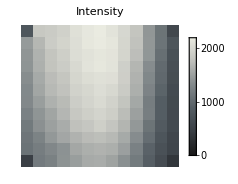
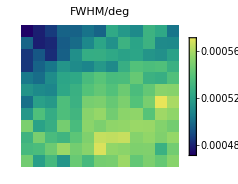
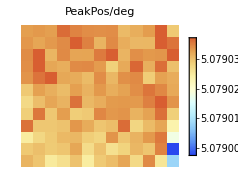

```mathematica
plotresGauss[res6,200,0.00005,0.00002]
```

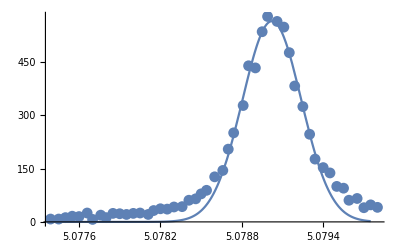

```mathematica
tilex=12; tiley=11;
Show[{ListPlot[res6[[tiley,tilex,1]]],Plot[res6[[tiley,tilex,2]][x],{x,theta[[1]],theta[[Length[theta]-1]]}]}]
```

```mathematica
res6[[tiley,tilex,2]]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 2067.29 | 25.4016 | 81.3843 | 7.89832×10^-18
CameraIfgPackage`Private`c | 5.07903 | 3.17496×10^-6 | 1.59971×10^6 | 2.39826×10^-69
CameraIfgPackage`Private`d | 0.000222003 | 3.87833×10^-6 | 57.2417 | 5.33337×10^-16

```mathematica
filename = "rocking_25May1709.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; Dimensions[img]
theta=LoadDatFile[StringTake[filename,StringLength[filename]-3]<>"dat"] [[2]]; Dimensions[theta]
```

{51,64,64}

{51}

```mathematica
ArrayPlot[img[[35]],ColorFunction->GrayLevel]  (* upside down! *)
```

-Graphics-

```mathematica
imglamella=img[[1;;Length[img],9;;56,8;;59]]; Dimensions[imglamella]
(*imglamella=img[[1;;Length[img],11;;54,10;;57]]; Dimensions[imglamella]*)
Row[{ArrayPlot[imglamella[[20]],ColorFunction->GrayLevel]}]
```

{51,48,52}

-Graphics-

```mathematica
res7=fitgridGauss[imglamella,theta,4,4,0,0.25]; Dimensions[res6]
```

{12,13,6}

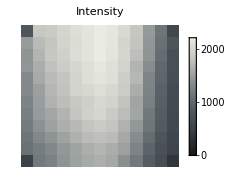
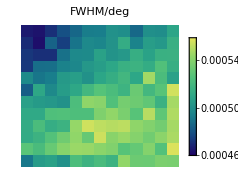
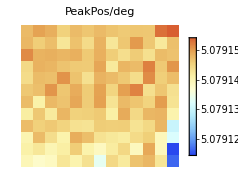

```mathematica
plotresGauss[res7,200,0.00005,0.00002]
```

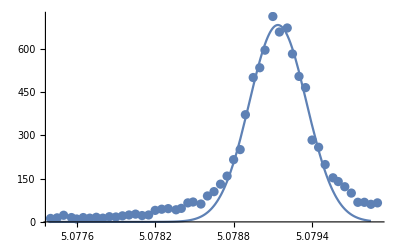

```mathematica
tilex=12; tiley=11;
Show[{ListPlot[res7[[tiley,tilex,1]]],Plot[res7[[tiley,tilex,2]][x],{x,theta[[1]],theta[[Length[theta]-1]]}]}]
```

```mathematica
filename = "rocking_25May1844.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; Dimensions[img]
theta=LoadDatFile[StringTake[filename,StringLength[filename]-3]<>"dat"] [[2]]; Dimensions[theta]
```

{51,64,64}

{51}

```mathematica
ArrayPlot[img[[35]],ColorFunction->GrayLevel]  (* upside down! *)
```

-Graphics-

```mathematica
imglamella=img[[1;;Length[img],9;;56,8;;59]]; Dimensions[imglamella]
(*imglamella=img[[1;;Length[img],11;;54,10;;57]]; Dimensions[imglamella]*)
Row[{ArrayPlot[imglamella[[20]],ColorFunction->GrayLevel]}]
```

{51,48,52}

-Graphics-

```mathematica
res8=fitgridGauss[imglamella,theta,4,4,0,0.25]; Dimensions[res6]
```

{12,13,6}

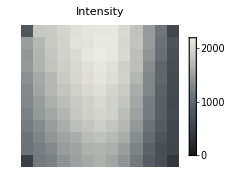
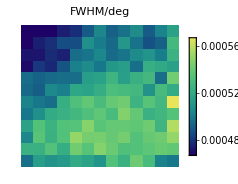
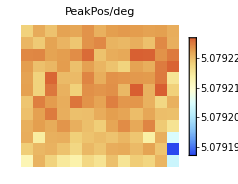

```mathematica
plotresGauss[res8,200,0.00005,0.00002]
```

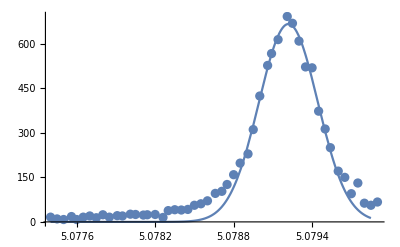

```mathematica
tilex=12; tiley=11;
Show[{ListPlot[res8[[tiley,tilex,1]]],Plot[res8[[tiley,tilex,2]][x],{x,theta[[1]],theta[[Length[theta]-1]]}]}]
```

```mathematica
filename = "rocking_25May2019.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; Dimensions[img]
theta=LoadDatFile[StringTake[filename,StringLength[filename]-3]<>"dat"] [[2]]; Dimensions[theta]
```

{51,64,64}

{51}

```mathematica
ArrayPlot[img[[35]],ColorFunction->GrayLevel]  (* upside down! *)
```

-Graphics-

```mathematica
imglamella=img[[1;;Length[img],9;;56,8;;59]]; Dimensions[imglamella]
(*imglamella=img[[1;;Length[img],11;;54,10;;57]]; Dimensions[imglamella]*)
Row[{ArrayPlot[imglamella[[20]],ColorFunction->GrayLevel]}]
```

{51,48,52}

-Graphics-

```mathematica
res9=fitgridGauss[imglamella,theta,4,4,0,0.25]; Dimensions[res6]
```

{12,13,6}

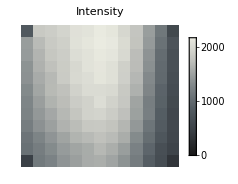
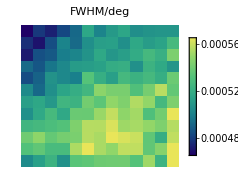
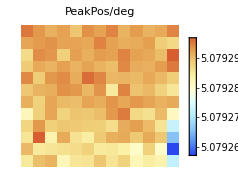

```mathematica
plotresGauss[res9,200,0.00005,0.00002]
```

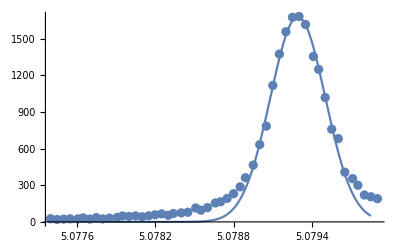

```mathematica
tilex=3; tiley=6;
Show[{ListPlot[res9[[tiley,tilex,1]]],Plot[res9[[tiley,tilex,2]][x],{x,theta[[1]],theta[[Length[theta]-1]]}]}]
```

```mathematica
filename = "rocking_25May2154.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; Dimensions[img]
theta=LoadDatFile[StringTake[filename,StringLength[filename]-3]<>"dat"] [[2]]; Dimensions[theta]
```

{51,64,64}

{51}

```mathematica
ArrayPlot[img[[35]],ColorFunction->GrayLevel]  (* upside down! *)
```

-Graphics-

```mathematica
imglamella=img[[1;;Length[img],9;;56,8;;59]]; Dimensions[imglamella]
(*imglamella=img[[1;;Length[img],11;;54,10;;57]]; Dimensions[imglamella]*)
Row[{ArrayPlot[imglamella[[20]],ColorFunction->GrayLevel]}]
```

{51,48,52}

-Graphics-

```mathematica
res10=fitgridGauss[imglamella,theta,4,4,0,0.25]; Dimensions[res6]
```

{12,13,6}

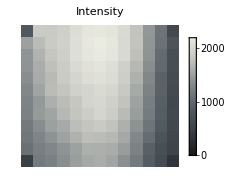
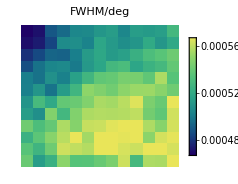
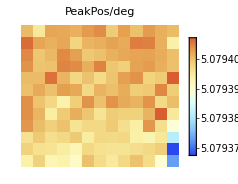

```mathematica
plotresGauss[res10,200,0.00005,0.00002]
```

```mathematica
filename = "rocking_25May2329.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; Dimensions[img]
theta=LoadDatFile[StringTake[filename,StringLength[filename]-3]<>"dat"] [[2]]; Dimensions[theta]
```

{51,64,64}

{51}

```mathematica
ArrayPlot[img[[35]],ColorFunction->GrayLevel]  (* upside down! *)
```

-Graphics-

```mathematica
imglamella=img[[1;;Length[img],9;;56,8;;59]]; Dimensions[imglamella]
(*imglamella=img[[1;;Length[img],11;;54,10;;57]]; Dimensions[imglamella]*)
Row[{ArrayPlot[imglamella[[20]],ColorFunction->GrayLevel]}]
```

{51,48,52}

-Graphics-

```mathematica
res11=fitgridGauss[imglamella,theta,4,4,0,0.25]; Dimensions[res6]
```

{12,13,6}

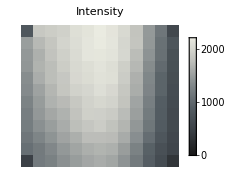
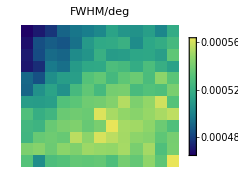
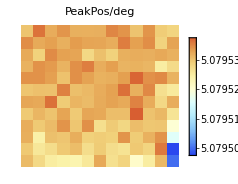

```mathematica
plotresGauss[res11,200,0.00005,0.00002]
```

```mathematica
filename = "rocking_26May0105.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; Dimensions[img]
theta=LoadDatFile[StringTake[filename,StringLength[filename]-3]<>"dat"] [[2]]; Dimensions[theta]
```

{51,64,64}

{51}

```mathematica
ArrayPlot[img[[35]],ColorFunction->GrayLevel]  (* upside down! *)
```

-Graphics-

```mathematica
imglamella=img[[1;;Length[img],9;;56,8;;59]]; Dimensions[imglamella]
(*imglamella=img[[1;;Length[img],11;;54,10;;57]]; Dimensions[imglamella]*)
Row[{ArrayPlot[imglamella[[20]],ColorFunction->GrayLevel]}]
```

{51,48,52}

-Graphics-

```mathematica
res12=fitgridGauss[imglamella,theta,4,4,0,0.25]; Dimensions[res6]
```

{12,13,6}

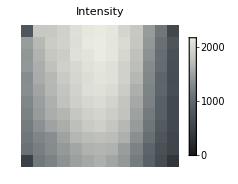
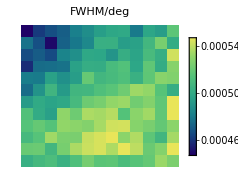
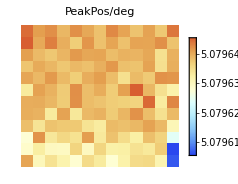

```mathematica
plotresGauss[res12,200,0.00005,0.00002]
```

```mathematica
filename = "rocking_26May0241.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; Dimensions[img]
theta=LoadDatFile[StringTake[filename,StringLength[filename]-3]<>"dat"] [[2]]; Dimensions[theta]
```

{51,64,64}

{51}

```mathematica
ArrayPlot[img[[35]],ColorFunction->GrayLevel]  (* upside down! *)
```

-Graphics-

```mathematica
imglamella=img[[1;;Length[img],9;;56,8;;59]]; Dimensions[imglamella]
(*imglamella=img[[1;;Length[img],11;;54,10;;57]]; Dimensions[imglamella]*)
Row[{ArrayPlot[imglamella[[20]],ColorFunction->GrayLevel]}]
```

{51,48,52}

-Graphics-

```mathematica
res13=fitgridGauss[imglamella,theta,4,4,0,0.25]; Dimensions[res6]
```

{12,13,6}

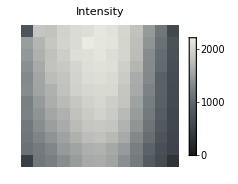
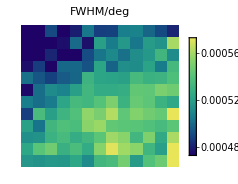
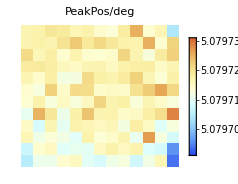

```mathematica
plotresGauss[res13,200,0.00005,0.00002]
```